loadDataFunc

```mathematica
Options[loadKappaCSV]={subtract1point5->True,earlyMLTStr->"20_50-23MLT",lateMLTStr->"23-1_50MLT",allMLTStr->"20_50-1_50MLT",printFName->False};
loadKappaCSV[EarlyOrLate_,BeamNoBeam_,Dst_,GoverK_,ventileOrDecile_,dateStr_,OptionsPattern[]]:=Module[{earlyNames,lateNames,allNames,dstStr,GoverKStr},
If[OptionValue[subtract1point5],subVal=1.5,subVal=0];
GoverKStr=(Switch[ToUpperCase[ventileOrDecile],"VENTILE","Ven","DECILE","Dec"])<>ToString[GoverK];
dstStr=If[Dst==0,"","-Dst"<>ToString[Dst]];
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
earlyNames={dateStr<>OptionValue[earlyMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[earlyMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
lateNames={dateStr<>OptionValue[lateMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[lateMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
allNames={dateStr<>OptionValue[allMLTStr]<>"-ionBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv",
dateStr<>OptionValue[allMLTStr]<>"-noBeam-data-allALT"<>dstStr<>"-BOTH-GK"<>GoverKStr<>"-Kchi2Max5_0-combo.csv"};
Switch[ToUpperCase[EarlyOrLate],
"EARLY",
names=earlyNames;,
"LATE",
names=lateNames;,
"ALL",
names=allNames;
];
Switch[BeamNoBeam//ToUpperCase,
"BEAM",
fName=names[[1]];,
"NOBEAM",
fName=names[[2]];
];
If[OptionValue[printFName],Print[fName]];
data=Import[inDir<>fName]//Flatten;
data=data-subVal
]
```

Now for Figure 3 stuff!

```mathematica
dateStr="20180516-";
```

```mathematica
allMLTStr="21-24MLT";
```

```mathematica
statType="ventile";
tile=10;
dstCutoff=-20;
```

```mathematica
If[ValueQ[allMLTStr],
Print["Using "<>allMLTStr<>" ..."];
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,subtract1point5->False,allMLTStr->allMLTStr];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,subtract1point5->False,allMLTStr->allMLTStr];
,
ABData=loadKappaCSV["All","Beam",dstCutoff,tile,statType,dateStr,subtract1point5->False];
ANData=loadKappaCSV["All","NoBeam",dstCutoff,tile,statType,dateStr,subtract1point5->False];];
```

Using 21-24MLT ...

```mathematica
ABDist=SmoothKernelDistribution[ABData];
ANDist=SmoothKernelDistribution[ANData];
```

```mathematica
lineVal[data_,κ_]:=Count[data,n_/;n≤ κ]/Length@data//N;
```

```mathematica
AB3=lineVal[ABData,3];
AN3=lineVal[ANData,3];
```

```mathematica
AB5=lineVal[ABData,5];
AN5=lineVal[ANData,5];
```

```mathematica
AB10=lineVal[ABData,10];
AN10=lineVal[ANData,10];
```

```mathematica
AB3line=Line[{{0,AB3},{1,AB3}}];
AN3line=Line[{{AN3,0},{AN3,1}}];
```

```mathematica
AB5line=Line[{{0,AB5},{1,AB5}}];
AN5line=Line[{{AN5,0},{AN5,1}}];
```

```mathematica
AB10line=Line[{{0,AB10},{1,AB10}}];
AN10line=Line[{{AN10,0},{AN10,1}}];
```

```mathematica
plotMin=0;plotMax=20;
```

```mathematica
lineVal[ABData,5.406]
```

0.539563

```mathematica
Median[ANData]
```

5.91268

```mathematica
Median[ABData]
```

5.15926

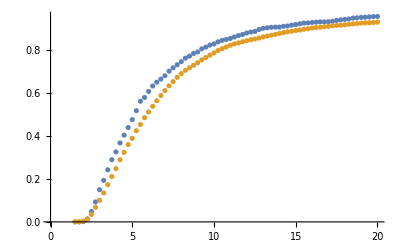

```mathematica
ListPlot[Table[{kVal,lineVal[#,kVal]},{kVal,1.5,20,0.25}]&/@{ABData,ANData}]
```

```mathematica
AB3Package={Directive[Orange,Thick,Dashed,Opacity[0.6]],AB3line,AN3line};
AB5Package={Directive[Brown,Thick,Dashed,Opacity[0.8]],AB5line,AN5line};
AB10Package={Directive[Purple,Thick,Dashed,Opacity[0.8]],AB10line,AN10line};
```

```mathematica
lineLeg=Framed[LineLegend[{AB3Package[[1]],AB5Package[[1]],AB10Package[[1]]},Style[#,FontSize->20]&/@{"κ = 3","κ = 5","κ = 10"}],RoundingRadius->5]
```

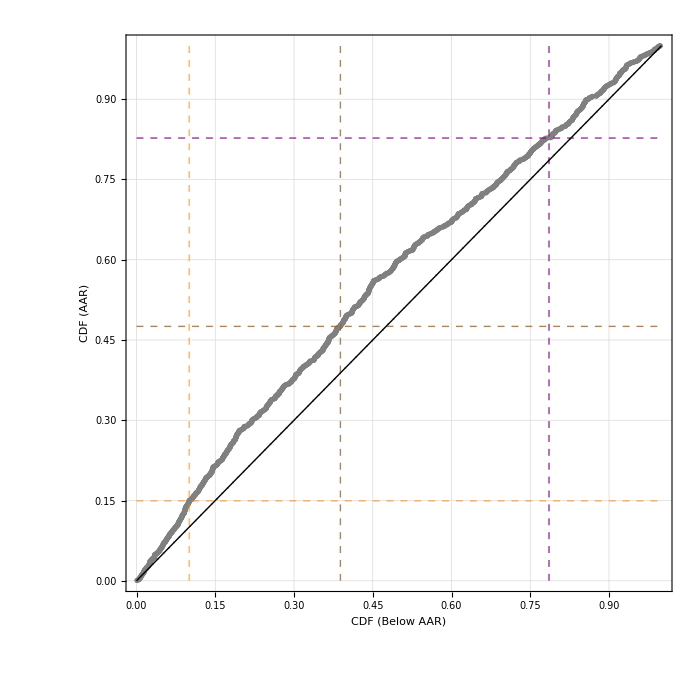

```mathematica
ProbabilityPlot[ABData,ANData,Frame->True,PlotStyle->Directive[Gray],FrameLabel->{"CDF (Below AAR)","CDF (AAR)"},FrameStyle->Directive[Black,FontSize->20],PlotTheme->"Detailed",AspectRatio->1,Epilog->{AB3Package,AB5Package,AB10Package,Inset[lineLeg,Scaled[{1.14,0.5}]]},ImageSize->700,PlotRangeClipping->False,ImagePadding->{{Automatic,135},{Automatic,Automatic}}]
```

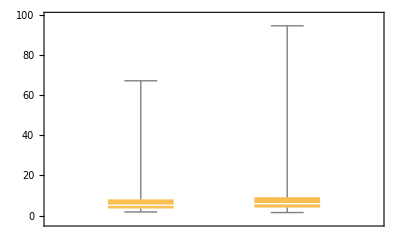

```mathematica
BoxWhiskerChart[{ABData,ANData}]
```

Now find dists

```mathematica
ABCandidateDists=FindDistribution[ABData-1.5,3,PerformanceGoal->"Quality"]
```

{InverseGaussianDistribution[5.91474,4.85168],MixtureDistribution[{0.945479,0.0545205},{InverseGaussianDistribution[4.69598,5.53395],LogNormalDistribution[3.1015,0.635059]}],FrechetDistribution[1.81788,3.83834,-1.10382]}

```mathematica
ANCandidateDists=FindDistribution[ANData-1.5,3,PerformanceGoal->"Quality"]
```

{FrechetDistribution[1.87361,4.97404,-1.6766],MixtureDistribution[{0.873806,0.126194},{ChiSquareDistribution[4.61695],LogNormalDistribution[3.11445,0.480648]}],MixtureDistribution[{0.851218,0.148782},{GammaDistribution[2.28599,1.94356],InverseGaussianDistribution[23.4097,71.0749]}]}

```mathematica
stripCandidates[candidateDists_]:=(If[ToString[Head[candidateDists[[#]]]]=="MixtureDistribution",((candidateDists[[#]])[[2]])[[1]],candidateDists[[#]]])&/@Range[Length@candidateDists];
```

```mathematica
ABCandidateDistsStrip=stripCandidates[ABCandidateDists]
```

{InverseGaussianDistribution[5.91474,4.85168],InverseGaussianDistribution[4.69598,5.53395],FrechetDistribution[1.81788,3.83834,-1.10382]}

```mathematica
ANCandidateDistsStrip=stripCandidates[ANCandidateDists]
```

{FrechetDistribution[1.87361,4.97404,-1.6766],ChiSquareDistribution[4.61695],GammaDistribution[2.28599,1.94356]}

#### Quantile Plots

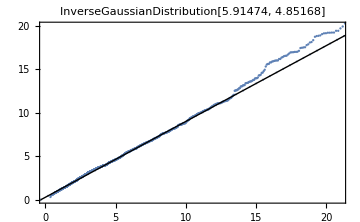
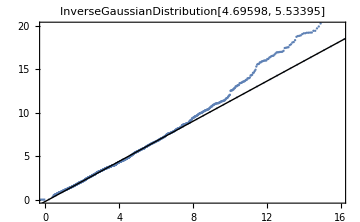
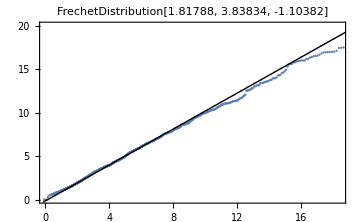

```mathematica
Table[QuantilePlot[ABData-1.5,dist,PlotLabel->ToString[dist],PlotRange->{0,20},ImageSize->Medium],{dist,ABCandidateDistsStrip}]
```

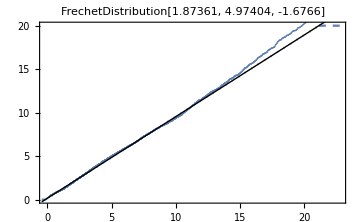
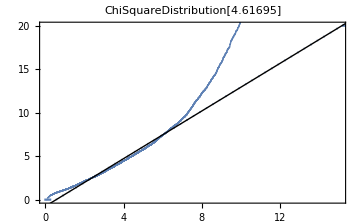
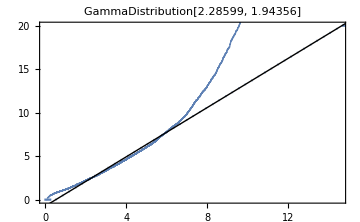

```mathematica
Table[QuantilePlot[ANData-1.5,dist,PlotLabel->ToString[dist],PlotRange->{0,20},ImageSize->Medium],{dist,ANCandidateDistsStrip}]
```

#### Probability Plots

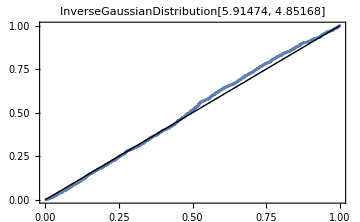
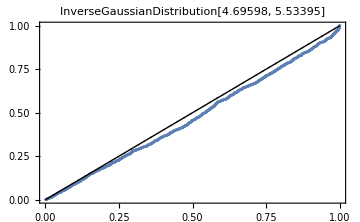
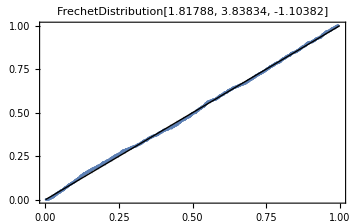

```mathematica
Table[ProbabilityPlot[ABData-1.5,dist,PlotLabel->ToString[dist],ImageSize->Medium],{dist,ABCandidateDistsStrip}]
```

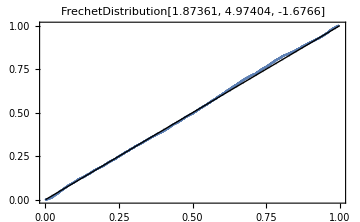
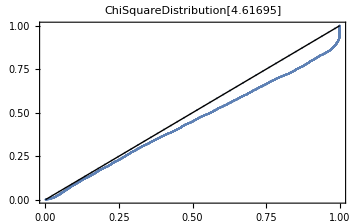
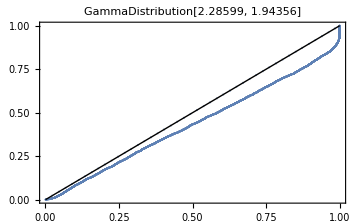

```mathematica
Table[ProbabilityPlot[ANData-1.5,dist,PlotLabel->ToString[dist],ImageSize->Medium],{dist,ANCandidateDistsStrip}]
```

Bunch of stat tests

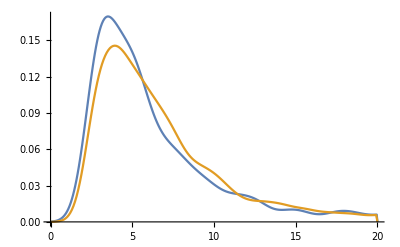

```mathematica
SmoothHistogram[{ABData,ANData},PlotRange->{{0,20},Full}]
```

```mathematica
funcs={KolmogorovSmirnovTest,AndersonDarlingTest,CramerVonMisesTest,MannWhitneyTest};
names = {"Kolmogorov-Smirnov","Anderson-Darling","Cramér–von Mises","Mann–Whitney U Test"};
headings=Style[#,Bold,FontSize->15]&/@{"Test","Test Statistic","p-value","Conclusion"};
signifLevel = 0.0001;
```

```mathematica
tmpANData=RandomChoice[ANData,Length[ABData]];
```

```mathematica
tmpANData=ANData;
```

```mathematica
{headings}~Join~Table[{names[[k]]}~Join~
(
If[ToString[funcs[[k]]]== ToString[MannWhitneyTest],
funcs[[k]][{ABData,tmpANData},"TestData"]~Join~{funcs[[k]][{ABData,tmpANData},"TestConclusion",SignificanceLevel->signifLevel]},
funcs[[k]][ABData,tmpANData,"TestData"]~Join~{funcs[[k]][ABData,tmpANData,"TestConclusion",SignificanceLevel->signifLevel]}]
),
{k,1,3}]//TableForm
```

Test | Test Statistic | p-value | Conclusion
Kolmogorov-Smirnov | 0.108573 | 1.30485×10^-12 | The null hypothesis that the datasets have the same distribution is rejected at the 0.01 percent level based on the Kolmogorov-Smirnov test.
Anderson-Darling | 25.8776 | 0. | The null hypothesis that the datasets have the same distribution is rejected at the 0.01 percent level based on the Anderson-Darling test.
Cramér–von Mises | 5.11343 | 1.7254×10^-12 | The null hypothesis that the datasets have the same distribution is rejected at the 0.01 percent level based on the Cramér-von Mises test.

```mathematica
k=4;
```

```mathematica
MWSignifLevel=.07;
```

```mathematica
MWMedianDiff=Median[ABData]-Median[ANData]
```

-0.75342

```mathematica
MWMedianDiff=Abs[MWMedianDiff]
```

0.75342

```mathematica
MWmedianList={0,-0.2,-0.4,-0.45,-0.5,-0.55,-0.65,-0.7,Median[ABData]-Median[ANData],-0.8};
MWSignifList={0.2,0.1,0.075,0.05,0.025,0.01};
```

```mathematica
MWTests=Table[MannWhitneyTest[{ABData,tmpANData},μ,"HypothesisTestData",SignificanceLevel->signif],{signif,MWSignifList},{μ,MWmedianList}]
```

{{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]},{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]},{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]},{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]},{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]},{HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…],HypothesisTestData[…]}}

```mathematica
Length[MWTests[[1]]]
```

10

```mathematica
Table[Through[MWTests[[k]]["TestConclusion"]],{k,1,Length[MWTests]}]
```

{{The null hypothesis that the median difference is 0 is rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is rejected at the 20. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is rejected at the 20. percent level based on the Mann-Whitney test.},{The null hypothesis that the median difference is 0 is rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is rejected at the 10. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is rejected at the 10. percent level based on the Mann-Whitney test.},{The null hypothesis that the median difference is 0 is rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is not rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is rejected at the 7.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is rejected at the 7.5 percent level based on the Mann-Whitney test.},{The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is not rejected at the 5. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is rejected at the 5. percent level based on the Mann-Whitney test.},{The null hypothesis that the median difference is 0 is rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is not rejected at the 2.5 percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is rejected at the 2.5 percent level based on the Mann-Whitney test.},{The null hypothesis that the median difference is 0 is rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.2 is rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.4 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.45 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.5 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.55 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.65 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.7 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.75342 is not rejected at the 1. percent level based on the Mann-Whitney test.,The null hypothesis that the median difference is -0.8 is not rejected at the 1. percent level based on the Mann-Whitney test.}}

```mathematica
MWTest["TestConclusion"]
```

The null hypothesis that the median difference is 0.75342 is rejected at the 1. percent level based on the Mann-Whitney test.

```mathematica
lens=Length/@{ABData,ANData}
```

{1466,6324}

```mathematica
Times@@lens
```

9270984

#### Calculate “Common language effect size” (https://en.wikipedia.org/wiki/Mann%E2%80%93Whitney_U_test#Common_language_effect_size)

```mathematica
effectSizeList=Table[Count[ABData,n_/;n<ANData[[k]]],{k,1,Length[ANData]}];
```

```mathematica
Total[effectSizeList]
```

5183857

```mathematica
favorable=Total[effectSizeList]/(Times@@lens)//N;
```

```mathematica
unfavorable=1-favorable;
```

```mathematica
rankBiserialCorr=favorable-unfavorable
```

0.118297

```mathematica
ANData[[1]]
```

2.72684